```mathematica
# u'(t) = sin(u(t)) + Sqrt(u(t)) - t;  Явен метод на Ойлер.
```

```mathematica
n = 100;
```

```mathematica
startInt = 0;
endInt = 5;
Ys = Table[0,{n+1}];
Ys[[1]] = 100;
h = 5./n;
```

```mathematica
t0 = 0;
```

```mathematica
For[i=2,i≤n+1,i++,Ys[[i]] = Ys[[i-1]]+ h*(Sin[Ys[[i-1]]] + Sqrt[Ys[[i-1]]] - (t0+h*(i-1)))];
```

```mathematica
Ys
```

```mathematica
Xs =Table[i*h,{i,0,n}];
```

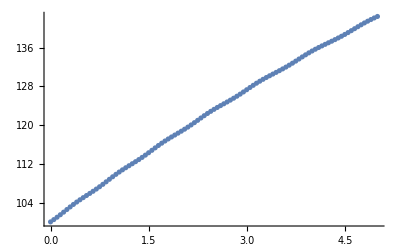

```mathematica
ListPlot[ Transpose[{Xs,Ys}]]
```